```mathematica
pde=D[u[x,t],t]-2D[u[x,t],x]==0;
sol=DSolve[{pde,u[x,0]==Cos[x]},u[x,t],{x,t}]
analyticPlot=Plot3D[u[x,t]/.sol,{x,-1,1},{t,-1,1}]
```

{{u[x,t]→Cos[2 t+x]}}

-Graphics3D-

```mathematica
AnalyticEval[x_,t_]:=N[Cos[2 t+x]];
L=10;
trail=Table[AnalyticEval[x,1],{x,0,1,1/L}]
```

{-0.416147,-0.504846,-0.588501,-0.666276,-0.737394,-0.801144,-0.856889,-0.904072,-0.942222,-0.970958,-0.989992}

```mathematica
ClearAll[numerical]
h=1/L;
τ=h*0.75;
Nm=Round[1/τ];
dt=τ/h;
numerical=Table[0,{t,Nm+1},{x,L+1}];
For[l=1,l<=L+1,l++,
numerical[[1,l]]=N[Cos[1/L*l]];
]
MatrixForm[numerical]
```

(0.995004 | 0.980067 | 0.955336 | 0.921061 | 0.877583 | 0.825336 | 0.764842 | 0.696707 | 0.62161 | 0.540302 | 0.453596
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
For[n = 1, n <= Nm+1, n++,
numerical[[n,L-1]] = Cos[1.0+2.0*n*τ]*(1.0-2.0*h^2)+(2.0*h-4.0*h^3/3)*Sin[1.0+2.0*n*τ];
 numerical[[n,L]] = Cos[1.0+2.0*n*τ]*(1.0-h^2/2)+(h-4.0*h^3/6)*Sin[1.0+2.0*n*τ];
numerical[[n,L+1]]=N[Cos[1+2*τ*n]];
 ]
MatrixForm[numerical]
```

(0.995004 | 0.980067 | 0.955336 | 0.921061 | 0.877583 | 0.825336 | 0.764842 | 0.696707 | 0.581653 | 0.497113 | 0.408487
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.453576 | 0.361875 | 0.267499
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.315312 | 0.21851 | 0.120503
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.169966 | 0.0702375 | -0.0291995
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0208041 | -0.0796122 | -0.178246
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.128825 | -0.227674 | -0.32329
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.275562 | -0.370623 | -0.461073
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.41611 | -0.505248 | -0.588501
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.547313 | -0.628526 | -0.702713
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.666224 | -0.73769 | -0.801144
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.770174 | -0.830286 | -0.881582
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.856827 | -0.904236 | -0.942222
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.924238 | -0.957878 | -0.981702
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.970892 | -0.990009 | -0.999135)

```mathematica
For[n=1,n≤ Nm,n++,
For[l=1,l≤ L-2,l++,
numerical[[n+1,l]]=numerical[[n,l]]+τ/(3h)(2numerical[[n,l+3]]-9numerical[[n,l+2]]+18numerical[[n,l+1]]-11numerical[[n,l]])+(2 τ^2)/h^2(-numerical[[n,l+3]]+4numerical[[n,l+2]]-5numerical[[n,l+1]]+2numerical[[n,l]])+(4 τ^3)/(3 h^3)(numerical[[n,l+3]]-3numerical[[n,l+2]]+3numerical[[n,l+1]]-numerical[[n,l]])
]
]
```

```mathematica
(*"Bug" fixing*)
```

```mathematica
τ=(1-(Nm)*τ);

For[l=1,l≤ L-2,l++,
numerical[[Nm+1,l]]=numerical[[Nm,l]]+τ/(3h)(2numerical[[Nm,l+3]]-9numerical[[Nm,l+2]]+18numerical[[Nm,l+1]]-11numerical[[Nm,l]])+(2 τ^2)/h^2(-numerical[[Nm,l+3]]+4numerical[[Nm,l+2]]-5numerical[[Nm,l+1]]+2numerical[[Nm,l]])+(4 τ^3)/(3 h^3)(numerical[[Nm,l+3]]-3numerical[[Nm,l+2]]+3numerical[[Nm,l+1]]-numerical[[Nm,l]]);
]
numerical[[Nm+1,L-1]] = Cos[3]*(1.0-2.0*h^2)+(2.0*h-4.0*h^3/3)*Sin[3];
 numerical[[Nm+1,L]] = Cos[3]*(1.0-h^2/2)+(h-4.0*h^3/6)*Sin[3];
numerical[[Nm+1,L+1]]=N[Cos[3]];
MatrixForm[numerical]
```

(0.995004 | 0.980067 | 0.955336 | 0.921061 | 0.877583 | 0.825336 | 0.764842 | 0.696707 | 0.581653 | 0.497113 | 0.408487
0.96891 | 0.939371 | 0.900445 | 0.852523 | 0.796082 | 0.734184 | 0.640205 | 0.537731 | 0.453576 | 0.361875 | 0.267499
0.921057 | 0.877578 | 0.825176 | 0.767479 | 0.689731 | 0.588354 | 0.49498 | 0.408364 | 0.315312 | 0.21851 | 0.120503
0.852266 | 0.797912 | 0.731335 | 0.640019 | 0.540745 | 0.451652 | 0.362474 | 0.26722 | 0.169966 | 0.0702375 | -0.0291995
0.766933 | 0.687721 | 0.590243 | 0.495567 | 0.407448 | 0.315352 | 0.218873 | 0.120238 | 0.0208041 | -0.0796122 | -0.178246
0.639948 | 0.54232 | 0.451347 | 0.361923 | 0.267521 | 0.16974 | 0.0706326 | -0.0294541 | -0.128825 | -0.227674 | -0.32329
0.496321 | 0.406849 | 0.315244 | 0.218925 | 0.120331 | 0.0206057 | -0.0792172 | -0.178484 | -0.275562 | -0.370623 | -0.461073
0.361475 | 0.267522 | 0.169841 | 0.0705449 | -0.0293343 | -0.129022 | -0.227286 | -0.323507 | -0.41611 | -0.505248 | -0.588501
0.219015 | 0.12033 | 0.0206298 | -0.0792794 | -0.178371 | -0.27575 | -0.370251 | -0.461263 | -0.547313 | -0.628526 | -0.702713
0.0705565 | -0.0293628 | -0.128983 | -0.227347 | -0.323398 | -0.416285 | -0.5049 | -0.588661 | -0.666224 | -0.73769 | -0.801144
-0.0792703 | -0.178388 | -0.275715 | -0.370307 | -0.461163 | -0.547472 | -0.628211 | -0.702839 | -0.770174 | -0.830286 | -0.881582
-0.227335 | -0.323415 | -0.416253 | -0.50495 | -0.588571 | -0.666363 | -0.737414 | -0.801232 | -0.856827 | -0.904236 | -0.942222
-0.370295 | -0.461177 | -0.547442 | -0.628253 | -0.702761 | -0.770289 | -0.830055 | -0.881632 | -0.924238 | -0.957878 | -0.981702
-0.416261 | -0.504938 | -0.588593 | -0.666331 | -0.737469 | -0.801147 | -0.856965 | -0.904002 | -0.942157 | -0.971025 | -0.989992)

-Graphics3D-

-Graphics3D-

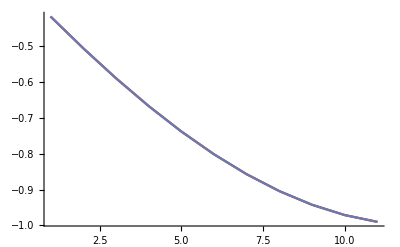

{{-0.416147,-0.504846,-0.588501,-0.666276,-0.737394,-0.801144,-0.856889,-0.904072,-0.942222,-0.970958,-0.989992},{-0.416261,-0.504938,-0.588593,-0.666331,-0.737469,-0.801147,-0.856965,-0.904002,-0.942157,-0.971025,-0.989992}}

```mathematica
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,1}]
ListPlot3D[numerical]
Show[ListLinePlot[trail,PlotStyle-> Red,PlotRange->{{0,12},{0,-1.2}}],ListLinePlot[numerical[[n,All]]]]
deltas=trail-numerical[[n,All]];
{trail,N[numerical[[n,All]]]}
```